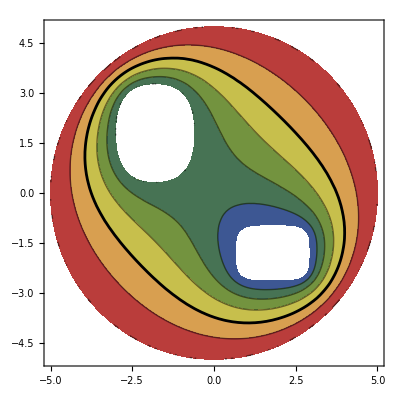

24.4978

```mathematica
(*Определения электродов*)electrodeCircle=x^2+y^2==25;
electrodeCurvedLeft=0.5*Abs[1.8+x]^2.5+0.3*Abs[-1.8+y]^2.5==0.8;
electrodeCurvedRight=0.3*Abs[-1.8+x]^4+Abs[1.8+y]^4==0.5;

(*Области,ограниченные электродами*)
regionCircle=ImplicitRegion[x^2+y^2<=25,{{x,-5,5},{y,-5,5}}];
regionCurvedLeft=ImplicitRegion[0.5*Abs[1.8+x]^2.5+0.3*Abs[-1.8+y]^2.5<=0.8,{{x,-5,5},{y,-5,5}}];
regionCurvedRight=ImplicitRegion[0.3*Abs[-1.8+x]^4+Abs[1.8+y]^4<=0.5,{{x,-5,5},{y,-5,5}}];

(*Свободная область без электродов*)
freeArea=RegionDifference[regionCircle,RegionUnion[regionCurvedLeft,regionCurvedRight]];

(*Граничные условия*)
boundaryConditions={DirichletCondition[u[x,y]==0,electrodeCircle],DirichletCondition[u[x,y]==-5,electrodeCurvedLeft],DirichletCondition[u[x,y]==-6,electrodeCurvedRight]};

(*Решение уравнения Лапласа*)
solveLaplace=NDSolve[{Laplacian[u[x,y],{x,y}]==0,boundaryConditions},u,{x,y}∈freeArea];

(*Визуализация решения*)
mainPlot=ContourPlot[u[x,y]/. First[solveLaplace],{x,y}∈freeArea,ColorFunction->"DarkRainbow"];
contourLine=ContourPlot[Evaluate[u[x,y]/. solveLaplace]==-2,{x,y}∈freeArea,Contours->1,ContourStyle->Black];
Show[mainPlot,contourLine]

(*Расчет длины линии уровня*)
discretizedContourLine=DiscretizeGraphics[contourLine];
lengthOfContourLine=RegionMeasure[discretizedContourLine]
```